```mathematica
f[x_]:=Expand[((x^3)-1)/(x-1)] (*el limite de la funcion f1 cuando x tiende a 0 es igual a 1 y coincide el valor de la funcion para ese punto; el limite cuando x tiende a 1 es 3 y es un hueco que no se ve en la grafica porque la funcion no esta definida en ese punto; el limite cuando x tiende a 2 tambien esta definido y coincide con el valor de la funcion para ese punto*)
```

```mathematica
Limit[f[x],x->0]
```

1

```mathematica
Limit[f[x],x->1]
```

3

```mathematica
Limit[f[x],x->2]
```

7

```mathematica
Limit[f[x],x->0];
f[0];
Limit[f[x],x->1];
f[1];
Limit[f[x],x->2];
f[2];
TableForm[Table[{x,f[x]},{x,0.99999,1.00001,0.000001}],{1,1/0.0000001}] (*La funcion es indeterminada cuando x tiende a 1 pero se ve que se va a acercando a 3*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

0.99999 | 2.99997
0.999991 | 2.99997
0.999992 | 2.99998
0.999993 | 2.99998
0.999994 | 2.99998
0.999995 | 2.99999
0.999996 | 2.99999
0.999997 | 2.99999
0.999998 | 2.99999
0.999999 | 3.
1. | Indeterminate
1. | 3.
1. | 3.00001
1. | 3.00001
1. | 3.00001
1.00001 | 3.00002
1.00001 | 3.00002
1.00001 | 3.00002
1.00001 | 3.00002
1.00001 | 3.00003
1.00001 | 3.00003

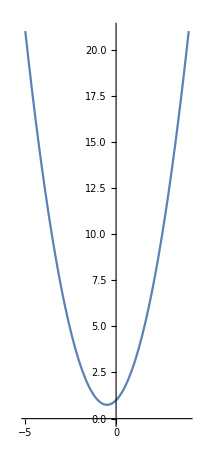

```mathematica
Plot[f[x], {x,-5,4}, AspectRatio->Automatic]
```

```mathematica
f1[x_]:=Expand[((x^2)-(5x)+6)/(x-3)] (*El limite cuando x tiende a 1 coincide con el valor de la funcion y es igual a -1; el limite cuando x tiende a 2 coincide tambien con el valor de la funcion y es igual a 7; y el limite cuando x tiende a 3 es igual a 13 y es un punto que no esta definido en la funcion*)

Limit[f1[x],x->1]
```

-1

```mathematica
Limit[f1[x],x->2]
```

0

```mathematica
Limit[f1[x],x->3]
```

1

```mathematica
Limit[f1[x],x->1];
f1[1];
Limit[f1[x],x->2];
f1[2];
Limit[f1[x],x->3];
f1[3];
TableForm[Table[{x,f1[x]},{x,2.99999,3.00001,0.000001}],{2,2/0.15}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

2.99999 | 0.99999
2.99999 | 0.999991
2.99999 | 0.999992
2.99999 | 0.999993
2.99999 | 0.999994
2.99999 | 0.999995
3. | 0.999996
3. | 0.999997
3. | 0.999998
3. | 0.999999
3. | Indeterminate
3. | 1.
3. | 1.
3. | 1.
3. | 1.
3.00001 | 1.00001
3.00001 | 1.00001
3.00001 | 1.00001
3.00001 | 1.00001
3.00001 | 1.00001
3.00001 | 1.00001

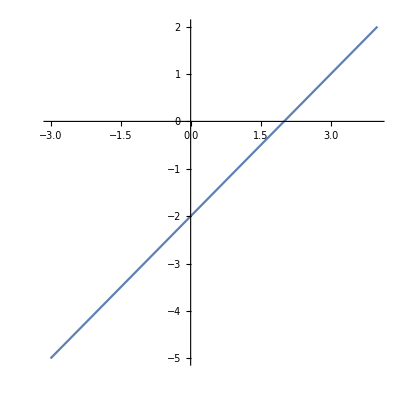

```mathematica
Plot[f1[x],{x,-3,4},AspectRatio->Automatic]
```

```mathematica
f2[x_]:=Expand[(x-4)/((Sqrt[x-3])-1)] (*el limite cuando x tiende a 3 es igual a 13, cuando tiene a 4 es igual a 21 y cuando tiende a 5 es igual a 31; solo en 4 la funcion esta indeterminada*)

Limit[f2[x],x->3]
```

1

```mathematica
Limit[f2[x],x->4]
```

2

```mathematica
Limit[f2[x],x->5]
```

1+√2

```mathematica
Limit[f2[x],x->1];
f2[1];
Limit[f2[x],x->4];
f2[4];
Limit[f2[x],x->5];
f2[5];
TableForm[Table[{x,f2[x]},{x,3.99999,4.00001,0.000001}],{2,2/0.15}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

3.99999 | 1.99999
3.99999 | 2.
3.99999 | 2.
3.99999 | 2.
3.99999 | 2.
3.99999 | 2.
4. | 2.
4. | 2.
4. | 2.
4. | 2.
4. | Indeterminate
4. | 2.
4. | 2.
4. | 2.
4. | 2.
4.00001 | 2.
4.00001 | 2.
4.00001 | 2.
4.00001 | 2.
4.00001 | 2.
4.00001 | 2.00001

```mathematica
Plot[f[x],{x,-5,4}, AspectRatio->Automatic]
```

-Graphics-

```mathematica
f3[x_]:=Expand[x/Abs[x]]

Limit[f3[x],x->-1]
```

-1

```mathematica
Limit[f3[x],x->0]
```

1

```mathematica
Limit[f3[x],x->1]
```

1

```mathematica
Limit[f[x],x->-1];
f[-1];
Limit[f[x],x->0];
f[0];
Limit[f[x],x->1];
f[1];
TableForm[Table[{x,f[x]},{x,-0.00001,0.00001,0.00001}],{1,1/0.0000001}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

-0.00001 | 0.99999
0. | 1.
0.00001 | 1.00001

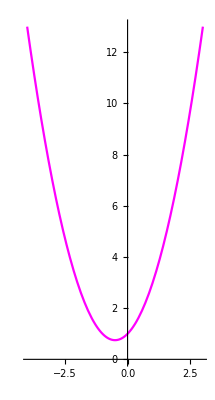

```mathematica
Plot[f[x],{x,-4,3},AspectRatio->Automatic, PlotStyle->Magenta]
```

```mathematica
f5[x_]:=If[x<2, x-2,-x^2];

Plot[Piecewise[{{-x^2,x>=2},{x-2,x<2}}],{x,-2,5}];

Plot [f5[x],{x,-5,5}];
f5[2];
f5[0];
Limit[f5[x],x->2];
f6[x]:=Piecewise[{{-x^2,x>=2},{x-2,x<2}}]
Limit[f6[x],x->2]
Limit[Piecewise[{{-x^2,x>=2},{x-2,x<2}}],x->2, Analytic->True];
Limit[Piecewise[{{-x^2,x>=2},{x-2,x<2}}],x->2, Direction->1];
Limit[Piecewise[{{-x^2,x>=2},{x-2,x<2}}],x->2, Direction->-1];
```

-4

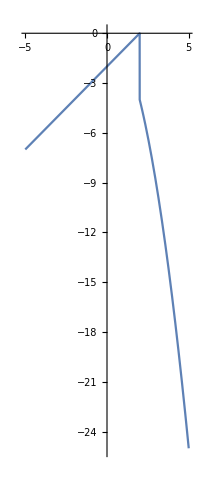

```mathematica
Plot[f5[x],{x,-5,5},AspectRatio->Automatic]
```